# Infinite 3D medium, Isotropic Point Source, Lambert Sphere Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine

### Namespace

```mathematica
Begin["inf3DisopointLambertSpherescatter`"]
```

inf3DisopointLambertSpherescatter`

## Util

```mathematica
SA[d_,r_]:=d Pi^(d/2)/Gamma[d/2+1] r^(d-1)
```

### Diffusion modes

```mathematica
diffusionMode[v_,d_,r_]:=(2 π)^(-d/2) r^(1-d/2) v^(-1-d/2) BesselK[1/2 (-2+d),r/v]
```

## Analytical solutions

### Fluence: exact solution

[Grosjean 1963 - A New Approximate One-Velocity Theory for Treating both Isotropic and Anisotropic Multiple Scattering Problems, p. 37]

```mathematica
ϕexactTruncatedFourierOrder7[r_,Σt_,c_]:=Exp[-r Σt]/(4 Pi r^2)+(c Σt)/(2 Pi^2 r)NIntegrate[u((1.3333333333333333 u^2-1.3999999999999997 u ArcTan[u]-2.337311630789803*^-16 u^3 ArcTan[u]+0.06666666666666664 ArcTan[u]^2+0.9999999999999998 u^2 ArcTan[u]^2-0.00030924479166666665 u^2 Hypergeometric2F1[7/2,4,15/2,-u^2]-0.0004216974431818181 u^4 Hypergeometric2F1[7/2,4,15/2,-u^2]-0.0001405658143939394 u^6 Hypergeometric2F1[7/2,4,15/2,-u^2]-6.693610209235209*^-6 u^8 Hypergeometric2F1[7/2,4,15/2,-u^2]+0.00032470703125 u ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]+0.000442782315340909 u^3 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]+0.00014759410511363638 u^5 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]+7.028290719696983*^-6 u^7 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]+8.916136286887371*^-22 u^9 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]-0.000015462239583333328 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]-0.00025301846590909086 u^2 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]-0.00032330137310606055 u^4 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]-0.0001057590413059163 u^6 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]-5.020207656926406*^-6 u^8 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]-3.242461239176438*^-8 u^6 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-5.558504981445322*^-8 u^8 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-1.0561159464746111*^-7 u^10 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-5.5585049814453225*^-8 u^12 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-1.228318152177984*^-7 u^14 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+9.00974926948953*^-8 u^16 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+3.40458430113526*^-8 u^5 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+5.836430230517588*^-8 u^7 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+1.1089217437983416*^-7 u^9 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+5.8364302305175895*^-8 u^11 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+1.484991523182093*^-8 u^13 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+8.559261806015054*^-8 u^15 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2-1.6212306195882188*^-9 u^4 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-2.7097711784545943*^-8 u^6 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-4.696936709321298*^-8 u^8 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-8.19879484763185*^-8 u^10 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-4.212420358438646*^-8 u^12 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-6.531243353198253*^-9 u^14 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+u^4 Hypergeometric2F1[5/2,3,11/2,-u^2]^2 (-8.527021919879064*^-6 u^2-5.684681279919375*^-6 u^4-0.000013713046947173927 u^6+0.000010078105316200553 u^8+8.953373015873015*^-6 u ArcTan[u]+5.968915343915344*^-6 u^3 ArcTan[u]+1.633099227345259*^-6 u^5 ArcTan[u]+9.574200050390523*^-6 u^7 ArcTan[u]-4.2635109599395304*^-7 ArcTan[u]^2-6.679500503905266*^-6 u^2 ArcTan[u]^2-4.310883303938859*^-6 u^4 ArcTan[u]^2-7.105851599899218*^-7 u^6 ArcTan[u]^2+(u^2 (1.9777028378625758*^-9+4.015336064751289*^-9 u^2+5.877383765896755*^-9 u^4+2.6417277537085793*^-9 u^6-1.7132059435166385*^-9 u^8-9.93635467705722*^-10 u^10-5.059418147570075*^-11 u^12)+(-2.0765879797557045*^-9 u-4.216102867988854*^-9 u^3-3.210481454233586*^-9 u^5-3.4113008279878395*^-9 u^7-3.2301953979921833*^-9 u^9-1.017552417685869*^-9 u^11-4.806447240191571*^-11 u^13) ArcTan[u]+(9.888514189312876*^-11+1.6840439316344963*^-9 u^2+3.1573326618604042*^-9 u^4+2.234547362260312*^-9 u^6+7.127435552037204*^-10 u^8+9.655451565322337*^-11 u^10+3.5672850610796814*^-12 u^12) ArcTan[u]^2) Hypergeometric2F1[7/2,4,15/2,-u^2]+2.3600816241260076*^-44 u^13 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2)+Hypergeometric2F1[5/2,3,11/2,-u^2] (-0.002199074074074074 u^2-0.0018849206349206352 u^4-0.00018849206349206342 u^6+0.002309027777777778 u ArcTan[u]+0.001979166666666667 u^3 ArcTan[u]+0.00019791666666666655 u^5 ArcTan[u]-0.00010995370370370366 ArcTan[u]^2-0.0017435515873015868 u^2 ArcTan[u]^2-0.0014231150793650794 u^4 ArcTan[u]^2-0.00014136904761904762 u^6 ArcTan[u]^2+(u^2 (5.100391529224537*^-7+1.1326843525940206*^-6 u^2+8.717032795401936*^-7 u^4+2.693713275174864*^-7 u^6+2.933434831279418*^-8 u^8+9.462693004127154*^-10 u^10)+(-5.355411105685764*^-7 u-1.1893185702237215*^-6 u^3-9.152884435172032*^-7 u^5-2.8283989389336067*^-7 u^7-3.080106572843393*^-8 u^9-9.935827654333515*^-10 u^11-1.088395542832931*^-25 u^13) ArcTan[u]+(2.550195764612268*^-8+4.3916358232154127*^-7 u^2+8.930984284225248*^-7 u^4+6.672460260310193*^-7 u^6+2.0349521305375447*^-7 u^8+2.2048074699616273*^-8 u^10+7.097019753095366*^-10 u^12) ArcTan[u]^2) Hypergeometric2F1[7/2,4,15/2,-u^2]+u^8 (u^2 (-1.2572808886602517*^-10-1.9158565922441929*^-10 u^2-2.8481561050051276*^-10 u^4-3.1895562657583395*^-11 u^6+1.1003902778341604*^-10 u^8+1.2736996735141446*^-11 u^10)+(1.3201449330932643*^-10 u+2.0116494218564024*^-10 u^3+1.10831883717337*^-10 u^5+1.6935163929863798*^-10 u^7+1.230654263323963*^-10 u^9+1.2100146898384375*^-11 u^11) ArcTan[u]+(-6.286404443301257*^-12-1.0387534961073984*^-10 u^2-1.4851879957793006*^-10 u^4-7.340125569035563*^-11 u^6-1.4428794960339077*^-11 u^8-8.980577776144653*^-13 u^10) ArcTan[u]^2) Hypergeometric2F1[7/2,4,15/2,-u^2]^2)+u^5 Hypergeometric2F1[3/2,2,7/2,-u^2]^2 (-0.007037037037037035 u+0.005555555555555555 u^3+0.0003518518518518523 ArcTan[u]+0.005277777777777776 u^2 ArcTan[u]+(1.6321252893518515*^-6 u+9.371054292929284*^-7 u^3-1.015197548400673*^-6 u^5-5.503635060926727*^-7 u^7-2.7890042538480034*^-8 u^9+(-8.160626446759271*^-8-1.3353752367424243*^-6 u^2-1.7063128025042084*^-6 u^4-5.58172718003447*^-7 u^6-2.6495540411556034*^-8 u^8) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2]+u^4 (1.7112989873431197*^-10 u+1.582629890550404*^-10 u^3-7.653973129212405*^-11 u^5-9.72738371752931*^-11 u^7-1.859452261650161*^-11 u^9-9.92590175258093*^-13 u^11+(-8.556494936715614*^-12-1.430157010851036*^-10 u^2-2.2777738766228217*^-10 u^4-1.175557630897335*^-10 u^6-1.892207737433678*^-11 u^8-9.429606664951885*^-13 u^10) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2]^2+Hypergeometric2F1[5/2,3,11/2,-u^2] (0.000011606224279835386 u+7.853835978835977*^-7 u^3-6.859016754850088*^-6 u^5-7.853835978835977*^-7 u^7-5.803112139917703*^-7 ArcTan[u]-9.202077821869489*^-6 u^2 ArcTan[u]-7.5108851410934715*^-6 u^4 ArcTan[u]-7.461144179894178*^-7 u^6 ArcTan[u]+(-2.6918733070907274*^-9 u-3.8528931681804386*^-9 u^3+1.1886193823517555*^-10 u^5+2.2104149917418506*^-9 u^7+9.675603596720017*^-10 u^9+1.1723225221779753*^-10 u^11+3.942788751719648*^-12 u^13+(1.345936653545366*^-10+2.3178077955859128*^-9 u^2+4.713575038896659*^-9 u^4+3.521576248497046*^-9 u^6+1.0740025133392595*^-9 u^8+1.1636483869241919*^-10 u^10+3.745649314133665*^-12 u^12) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2]))+Hypergeometric2F1[3/2,2,7/2,-u^2] (-0.07916666666666665 u^2-0.026388888888888882 u^4+0.08312499999999999 u ArcTan[u]+0.027708333333333324 u^3 ArcTan[u]+3.652049423109067*^-18 u^5 ArcTan[u]-0.003958333333333333 ArcTan[u]^2-0.06069444444444443 u^2 ArcTan[u]^2-0.019791666666666662 u^4 ArcTan[u]^2+0.000018361409505208334 u^2 Hypergeometric2F1[7/2,4,15/2,-u^2]+0.00003115875552398989 u^4 Hypergeometric2F1[7/2,4,15/2,-u^2]+0.0000166921904592803 u^6 Hypergeometric2F1[7/2,4,15/2,-u^2]+3.179464849386724*^-6 u^8 Hypergeometric2F1[7/2,4,15/2,-u^2]+1.3247770205778017*^-7 u^10 Hypergeometric2F1[7/2,4,15/2,-u^2]-0.00001927947998046875 u ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]-0.00003271669330018938 u^3 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]-0.000017526799982244312 u^5 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]-3.33843809185606*^-6 u^7 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]-1.391015871606694*^-7 u^9 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]+9.180704752604166*^-7 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]+0.000015328994905105745 u^2 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]+0.000024203676165956436 u^4 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]+0.000012678116086929564 u^6 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]+2.3912225221429324*^-6 u^8 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]+9.935827654333512*^-8 u^10 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]+1.92521136076101*^-9 u^6 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+3.94209945298683*^-9 u^8 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+2.844598010593818*^-9 u^10 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+8.643806109539228*^-10 u^12 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-6.667641786448301*^-9 u^14 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+3.095559344393466*^-9 u^16 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+1.7831795429198027*^-9 u^18 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-2.0214719287990605*^-9 u^5 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2-4.1392044256361715*^-9 u^7 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2-2.9868279111235095*^-9 u^9 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2-9.075996415016188*^-10 u^11 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+2.2494161267546796*^-10 u^13 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+5.190045858207257*^-9 u^15 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+1.6940205657738122*^-9 u^17 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+9.626056803805048*^-11 u^4 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+1.6410134932200989*^-9 u^6 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+3.0988044902698135*^-9 u^8 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+2.1766675384930604*^-9 u^10 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+6.537074820477894*^-10 u^12 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+8.156609765183379*^-11 u^14 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+3.536102499356957*^-12 u^16 ArcTan[u]^2 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+u^9 Hypergeometric2F1[5/2,3,11/2,-u^2]^2 (-7.5795750398925*^-7 u+3.45735001819658*^-7 u^3+1.994625010498026*^-7 u^5+3.789787519946254*^-8 ArcTan[u]+5.81100753058425*^-7 u^2 ArcTan[u]+1.8948937599731244*^-7 u^4 ArcTan[u]+(1.7579580781000673*^-10 u+1.5953399464735848*^-10 u^3-7.570154403301727*^-11 u^5-9.572840753381547*^-11 u^7-2.2763868179240637*^-11 u^9-1.0013431750399107*^-12 u^11+(-8.789790390500344*^-12-1.4676286379289958*^-10 u^2-2.3173083756773613*^-10 u^4-1.2138281967833794*^-10 u^6-2.289404279199582*^-11 u^8-9.51276016287915*^-13 u^10) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2])+Hypergeometric2F1[5/2,3,11/2,-u^2] (0.00013057002314814813 u^2+0.00015544050374779537 u^4+0.00004849743716931215 u^6+3.730572089947088*^-6 u^8-0.00013709852430555554 u ArcTan[u]-0.00016321252893518516 u^3 ArcTan[u]-0.00005092230902777777 u^5 ArcTan[u]-3.9171006944444275*^-6 u^7 ArcTan[u]-4.458068143443686*^-22 u^9 ArcTan[u]+6.528501157407406*^-6 ArcTan[u]^2+0.00010569954254850087 u^2 ArcTan[u]^2+0.00011900524966931214 u^4 ArcTan[u]^2+0.000036559606481481464 u^6 ArcTan[u]^2+2.7979290674603167*^-6 u^8 ArcTan[u]^2+(u^2 (-3.028357470477069*^-8-7.734765833686019*^-8 u^2-7.417509336778895*^-8 u^4-3.324638331225041*^-8 u^6-7.073034454855736*^-9 u^8-6.36760383402723*^-10 u^10-1.8728246570668323*^-11 u^12)+(3.1797753440009226*^-8 u+8.121504125370321*^-8 u^3+7.788384803617842*^-8 u^5+3.490870247786293*^-8 u^7+7.426686177598523*^-9 u^9+6.685984025728589*^-10 u^11+1.966465889920171*^-11 u^13+1.700618035676455*^-27 u^15) ArcTan[u]+(-1.5141787352385342*^-9-2.658006394542103*^-8 u^2-6.171949842103459*^-8 u^4-5.7293639191454246*^-8 u^6-2.5288439206930598*^-8 u^8-5.33661386031194*^-9 u^10-4.785066998805757*^-10 u^12-1.4046184928001245*^-11 u^14) ArcTan[u]^2) Hypergeometric2F1[7/2,4,15/2,-u^2]+u^13 (-1.1175830121424458*^-11 u-4.481535888290506*^-12 u^3+6.352577121651799*^-12 u^5+2.957813686271736*^-12 u^7+2.520863937163412*^-13 u^9+(5.587915060712234*^-13+9.047100574486466*^-12 u^2+1.0185970882098291*^-11 u^4+3.129232433998848*^-12 u^6+2.3948207403052407*^-13 u^8) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2]^2)))/(u (0.06333333333333331 u+1. u^3-0.06333333333333331 ArcTan[u]-0.9499999999999998 u^2 ArcTan[u]-0.000014689127604166663 u Hypergeometric2F1[7/2,4,15/2,-u^2]-0.0002519642223011364 u^3 Hypergeometric2F1[7/2,4,15/2,-u^2]-0.00032294995857007575 u^5 Hypergeometric2F1[7/2,4,15/2,-u^2]-0.00010574230728039322 u^7 Hypergeometric2F1[7/2,4,15/2,-u^2]-5.020207656926407*^-6 u^9 Hypergeometric2F1[7/2,4,15/2,-u^2]+0.000014689127604166663 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]+0.00024036754261363635 u^2 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]+0.00030713630445075753 u^4 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]+0.00010047108924062049 u^6 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]+4.769197274080086*^-6 u^8 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]-1.5401690886088079*^-9 u^5 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-2.695874916000981*^-8 u^7 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-4.670533810659433*^-8 u^9 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-8.184898585178239*^-8 u^11 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-4.7523298583685345*^-8 u^13 Hypergeometric2F1[7/2,4,15/2,-u^2]^2-8.784423051034127*^-8 u^15 Hypergeometric2F1[7/2,4,15/2,-u^2]^2+1.5401690886088079*^-9 u^4 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+2.5742826195318646*^-8 u^6 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+4.462089873855233*^-8 u^8 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+7.788855105250257*^-8 u^10 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+4.001799340516714*^-8 u^12 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+6.204681185538341*^-9 u^14 ArcTan[u] Hypergeometric2F1[7/2,4,15/2,-u^2]^2+u^4 Hypergeometric2F1[5/2,3,11/2,-u^2]^2 (-4.050335411942554*^-7 u-6.665288800705468*^-6 u^3-4.914880689930294*^-6 u^5-9.806075207860919*^-6 u^7+4.050335411942554*^-7 ArcTan[u]+6.3455254787100024*^-6 u^2 ArcTan[u]+4.095339138741916*^-6 u^4 ArcTan[u]+6.750559019904257*^-7 u^6 ArcTan[u]+(9.394088479847233*^-11 u+1.6740055914726182*^-9 u^3+3.290677777443564*^-9 u^5+4.533519892723724*^-9 u^7+3.6530069210974262*^-9 u^9+1.0584729323733594*^-9 u^11+4.9228533842899604*^-11 u^13+(-9.394088479847233*^-11-1.5998417350527715*^-9 u^2-2.9994660287673843*^-9 u^4-2.1228199941472967*^-9 u^6-6.771063774435344*^-10 u^8-9.172678987056221*^-11 u^10-3.3889208080256974*^-12 u^12) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2]-2.2420775429197073*^-44 u^13 Hypergeometric2F1[7/2,4,15/2,-u^2]^2)+Hypergeometric2F1[5/2,3,11/2,-u^2] (-0.00010445601851851848 u-0.0017388392857142856 u^3-0.001422643849206349 u^5-0.0001413690476190476 u^7+0.00010445601851851848 ArcTan[u]+0.0016563740079365075 u^2 ArcTan[u]+0.0013519593253968254 u^4 ArcTan[u]+0.00013430059523809523 u^6 ArcTan[u]+(2.4226859763816547*^-8 u+4.3633187144005633*^-7 u^3+8.909191702236746*^-7 u^5+6.665725977122258*^-7 u^7+2.0342187718297252*^-7 u^9+2.204570902636524*^-8 u^11+7.097019753095367*^-10 u^13+(-2.4226859763816547*^-8-4.172054032054642*^-7 u^2-8.484435070013986*^-7 u^4-6.338837247294684*^-7 u^6-1.9332045240106675*^-7 u^8-2.094567096463546*^-8 u^10-6.742168765440598*^-10 u^12) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2]+u^8 (-5.972084221136194*^-12 u-1.0339638546267878*^-10 u^3-1.572179859170888*^-10 u^5-2.151267471016198*^-10 u^7-1.3014353960596295*^-10 u^9-1.2393197331079623*^-11 u^11+(5.972084221136194*^-12+9.868158213020285*^-11 u^2+1.4109285959903355*^-10 u^4+6.973119290583785*^-11 u^6+1.3707355212322124*^-11 u^8+8.531548887337421*^-13 u^10) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2]^2)+u^5 Hypergeometric2F1[3/2,2,7/2,-u^2]^2 (-0.00033425925925925973-0.005013888888888888 u^2+(7.752595124421308*^-8+1.268606474905303*^-6 u^2+1.620997162378998*^-6 u^4+5.302640821032747*^-7 u^6+2.5170763390978234*^-8 u^8) Hypergeometric2F1[7/2,4,15/2,-u^2]+u^4 (8.128670189879833*^-12+1.3586491603084844*^-10 u^2+2.1638851827916808*^-10 u^4+1.1167797493524682*^-10 u^6+1.7975973505619944*^-11 u^8+8.95812633170429*^-13 u^10) Hypergeometric2F1[7/2,4,15/2,-u^2]^2+Hypergeometric2F1[5/2,3,11/2,-u^2] (5.512956532921818*^-7+8.741973930776015*^-6 u^2+7.135340884038798*^-6 u^4+7.08808697089947*^-7 u^6+(-1.2786398208680978*^-10-2.2019174058066174*^-9 u^2-4.477896286951826*^-9 u^4-3.345497436072194*^-9 u^6-1.0203023876722966*^-9 u^8-1.1054659675779824*^-10 u^10-3.558366848426982*^-12 u^12) Hypergeometric2F1[7/2,4,15/2,-u^2]))+Hypergeometric2F1[3/2,2,7/2,-u^2] (-0.0037604166666666662 u-0.06062847222222222 u^3-0.01979166666666667 u^5+0.0037604166666666662 ArcTan[u]+0.057659722222222216 u^2 ArcTan[u]+0.01880208333333333 u^4 ArcTan[u]+(8.721669514973958*^-7 u+0.000015251098016295774 u^3+0.000024161945689808236 u^5+0.000012670167424806096 u^7+2.3908913278877878*^-6 u^9+9.935827654333514*^-8 u^11+(-8.721669514973958*^-7-0.00001456254515985046 u^2-0.000022993492357658616 u^4-0.000012044210282583086 u^6-2.271661396035786*^-6 u^8-9.439036271616837*^-8 u^10) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2]+u^4 (9.144753963614797*^-11 u+1.6311582445876322*^-9 u^3+3.091692995243329*^-9 u^5+2.1745065869656758*^-9 u^7+3.315724733591484*^-10 u^9-4.853692270977536*^-9 u^11-1.6057834349857647*^-9 u^13+(-9.144753963614797*^-11-1.558962818559094*^-9 u^2-2.943864265756323*^-9 u^4-2.0678341615684074*^-9 u^6-6.210221079454*^-10 u^8-7.74877927692421*^-11 u^10-3.359297374389109*^-12 u^12) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2]^2+u^9 Hypergeometric2F1[5/2,3,11/2,-u^2]^2 (-3.600298143948941*^-8-5.520457154055038*^-7 u^2-1.8001490719744684*^-7 u^4+(8.350300870975327*^-12+1.394247206032546*^-10 u^2+2.2014429568934935*^-10 u^4+1.1531367869442106*^-10 u^6+2.174934065239603*^-11 u^8+9.037122154735193*^-13 u^10) Hypergeometric2F1[7/2,4,15/2,-u^2])+Hypergeometric2F1[5/2,3,11/2,-u^2] (6.202076099537036*^-6 u+0.0001053109412891314 u^3+0.00011888400607638889 u^5+0.000036550280051256606 u^7+2.797929067460317*^-6 u^9-6.202076099537036*^-6 ArcTan[u]-0.00010041456542107584 u^2 ArcTan[u]-0.00011305498718584654 u^4 ArcTan[u]-0.000034731626157407394 u^6 ArcTan[u]-2.658032614087301*^-6 u^8 ArcTan[u]+(-1.4384697984766076*^-9 u-2.638669479957888*^-8 u^3-6.153406068761513*^-8 u^5-5.721052323317363*^-8 u^7-2.5270756620793458*^-8 u^9-5.335021959353433*^-9 u^11-4.784598792641491*^-10 u^13-1.4046184928001247*^-11 u^15+(1.4384697984766076*^-9+2.525106074814998*^-8 u^2+5.863352349998286*^-8 u^4+5.4428957231881536*^-8 u^6+2.402401724658407*^-8 u^8+5.069783167296343*^-9 u^10+4.54581364886547*^-10 u^12+1.3343875681601184*^-11 u^14) ArcTan[u]) Hypergeometric2F1[7/2,4,15/2,-u^2]+u^13 (-5.308519307676622*^-13-8.594745545762143*^-12 u^2-9.676672337993377*^-12 u^4-2.9727708122989056*^-12 u^6-2.2750797032899787*^-13 u^8) Hypergeometric2F1[7/2,4,15/2,-u^2]^2)))))Sin[r Σt u],{u,0,Infinity},Method->"LevinRule"]
```

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_LSscatter*"];
```

```mathematica
index[x_]:=Module[{data,α,Σt},
data=Import[x,"Table"];
Σt=data[[1,13]];
α=data[[2,3]];
{α,Σt,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
mfps=Union[#[[2]]&/@simulations]
```

{0.3,1}

```mathematica
numcollorders=simulations[[1]][[3]][[2,13]];
maxr=simulations[[1]][[3]][[2,5]];dr=simulations[[1]][[3]][[2,7]];
numr=Floor[maxr/dr];
```

## Compare MC and deterministic

### Fluence - Exact solution comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

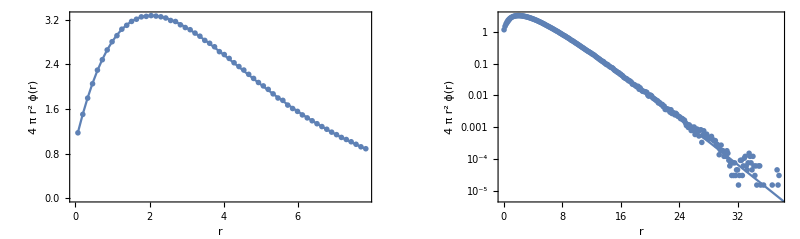

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[-1]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsFluence=ppoints[data[[6]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexactTruncatedFourierOrder7[#[[1]],1/mfp,c]}]& /@pointsFluence[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexactTruncatedFourierOrder7[#[[1]],1/mfp,c]}]& /@pointsFluence[[1;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution\nInfinite 3D, isotropic point source, Lambert-Sphere scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### Compare moments of ϕ

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

#### mfp 1

```mathematica
mfp=1;
sims1=Select[simulations,#[[2]]==mfp&];
```

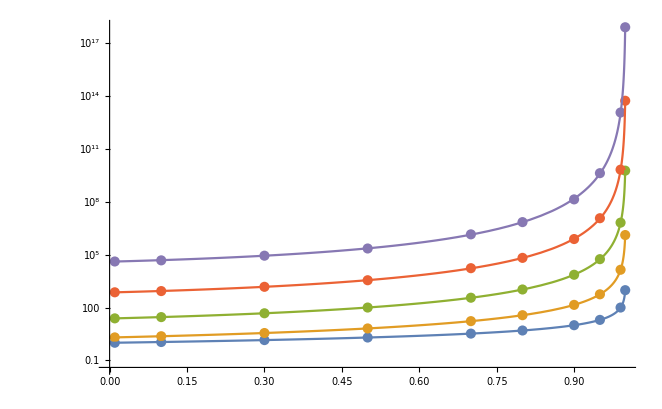

```mathematica
Show[
ListLogPlot[{
{#[[-1,2,3]],#[[-1,10,1]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,3]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,5]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,7]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,9]]}&/@sims1
}],
LogPlot[{mfp/(1-c),-3!mfp mfp^2/((-3-(4 c)/3) (-1+c)^2),5!mfp((9-(69 c)/16) mfp^4)/((-3-(4 c)/3)^2 (-5+(5 c)/16) (-1+c)^3),mfp 7!((-675+(5691 c)/8-(36399 c^2)/256-48 c^3) mfp^6)/(7 (-3-(4 c)/3)^3 (-5+(5 c)/16)^2 (-1+c)^4),mfp 9!((-496125+(52729425 c)/64-(367391171 c^2)/1024-(1099685881 c^3)/16384+(11363604819 c^4)/262144+(312487 c^5)/32-329 c^6) mfp^8)/(49 (-3-(4 c)/3)^4 (-9+c/64) (-5+(5 c)/16)^3 (-1+c)^5)},{c,0,.999},PlotRange->All]
]
```

#### mfp 0.3

```mathematica
mfp=0.3;
sims1=Select[simulations,#[[2]]==mfp&];
```

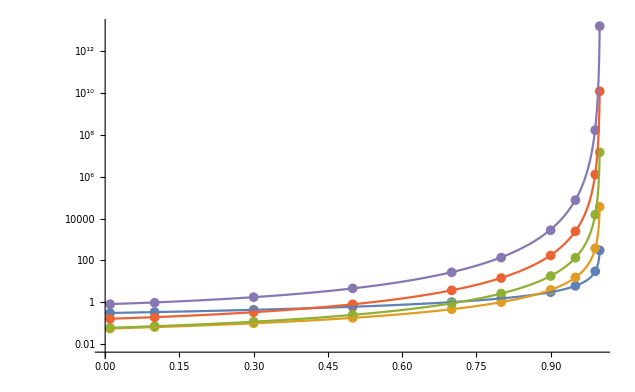

```mathematica
Show[
ListLogPlot[{
{#[[-1,2,3]],#[[-1,10,1]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,3]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,5]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,7]]}&/@sims1,
{#[[-1,2,3]],#[[-1,10,9]]}&/@sims1
}],
LogPlot[{mfp/(1-c),-3!mfp mfp^2/((-3-(4 c)/3) (-1+c)^2),5!mfp((9-(69 c)/16) mfp^4)/((-3-(4 c)/3)^2 (-5+(5 c)/16) (-1+c)^3),mfp 7!((-675+(5691 c)/8-(36399 c^2)/256-48 c^3) mfp^6)/(7 (-3-(4 c)/3)^3 (-5+(5 c)/16)^2 (-1+c)^4),mfp 9!((-496125+(52729425 c)/64-(367391171 c^2)/1024-(1099685881 c^3)/16384+(11363604819 c^4)/262144+(312487 c^5)/32-329 c^6) mfp^8)/(49 (-3-(4 c)/3)^4 (-9+c/64) (-5+(5 c)/16)^3 (-1+c)^5)},{c,0,.999},PlotRange->All]
]
```